```mathematica
Eigenvalues[({{x y, 2}, {2, -(x^2+y^2)}})]//MatrixForm
Eigenvalues[({{x y, 2}, {2, -(x^2+y^2)}})]//FullSimplify//MatrixForm
```

(1/2 (-x^2+x y-y^2-√(16+x^4+2 x^3 y+3 x^2 y^2+2 x y^3+y^4))
1/2 (-x^2+x y-y^2+√(16+x^4+2 x^3 y+3 x^2 y^2+2 x y^3+y^4)))

(1/2 (-x^2+x y-y^2-√(16+(x^2+x y+y^2)^2))
1/2 (-x^2+x y-y^2+√(16+(x^2+x y+y^2)^2)))

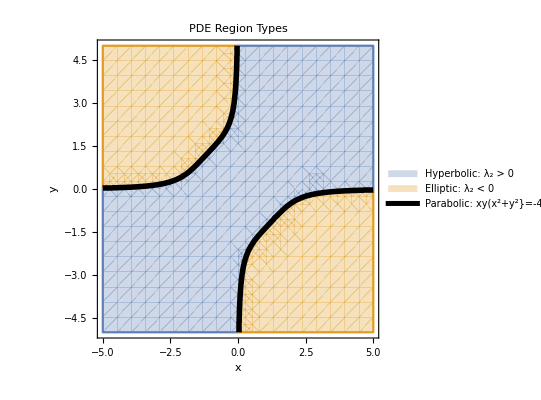

```mathematica
Show[{
RegionPlot[{1/2 (-x^2+x y-y^2+√(16+(x^2+x y+y^2)^2))>0,1/2 (-x^2+x y-y^2+√(16+(x^2+x y+y^2)^2))<0},{x,-5,5},{y,-5,5},
PlotLegends->{"Hyperbolic: λ_2 > 0","Elliptic: λ_2 < 0"},
FrameLabel->{x,y},
PlotLabel->"PDE Region Types"],
ContourPlot[{x y(x^2+y^2)+4==0,1==1},{x,-5,5},{y,-5,5},
PlotLegends->{"Parabolic: xy(x^2+y^2}=-4"},
ContourStyle->{Directive[Black,Thickness[0.01]],Blue}]}]
```